Do the following tasks using Mathematica.
If a projectile is fired with an initial velocity of v0 meters per second at an
angle α above the horizontal and air resistance is assumed to be negligible,
then it’s position after t seconds is given by the parametric equations
x = (v_0 cos α)t and y = (v_0 sin α)t -1/2g t^2. Also v_x = dx/dt and v_y = dy/dt
(a) Find v_x and v_y . If a gun is fired with α = 300 and v0 = 500m/s when will
the bullet hit the ground? How far from the gun will it hit the ground?
What is the maximum height reached by the bullet?
Hint: The Bullet reaches the ground when y=0 and it is at
maximum height when v_y = 0

```mathematica
x = Subscript[v, 0] Cos[α] t;
```

```mathematica
y = Subscript[v, 0] Sin[α]t - 1/2 g t^2;
```

```mathematica
vx = D[x,t]
```

Cos[α] v_0

```mathematica
vy = D[y,t]
```

-g t+Sin[α] v_0

```mathematica
α = 30 °;
Subscript[v, 0] = 500;
g = 9.8;
```

```mathematica
Solve[y== 0 , t]
```

{{t→0.+0. ⅈ},{t→51.0204}}

After 51.0204 sec bullet will hit the ground

```mathematica
x/. t -> 51.0204081632653
```

22092.5

Bullet hit the ground 22092.5 meters far from the gun

```mathematica
Solve[vy == 0, t]
```

{{t→25.5102}}

```mathematica
y/.t -> 25.51020408163265
```

3188.78

Maximum height reached by the bullet is 3188.78 meters


(b) Plot the path of the projectile for v_0 = 500m/s and α = 30 °, 45° and 60° in a single graph.

```mathematica
Solve[Subscript[v, 0] Sin[30 °]t - 1/2 g t^2 == 0 , t]
```

{{t→0.+0. ⅈ},{t→51.0204}}

```mathematica
Solve[Subscript[v, 0] Sin[45 °]t - 1/2 g t^2 == 0 , t]
```

{{t→0.+0. ⅈ},{t→72.1538}}

```mathematica
Solve[Subscript[v, 0] Sin[60 °]t - 1/2 g t^2 == 0 , t]
```

{{t→0.+0. ⅈ},{t→88.3699}}

```mathematica
a = ParametricPlot[{Subscript[v, 0] Cos[30 °] t, Subscript[v, 0] Sin[30 °]t - 1/2 g t^2 },{t,0 , 51.0204081632653}];
b = ParametricPlot[{Subscript[v, 0] Cos[45°] t, Subscript[v, 0] Sin[45 °]t - 1/2 g t^2 },{t,0 , 72.15375318230076 }];
c = ParametricPlot[{Subscript[v, 0] Cos[60°] t, Subscript[v, 0] Sin[60 °]t - 1/2 g t^2 },{t,0 , 88.36993916167741 }];
```

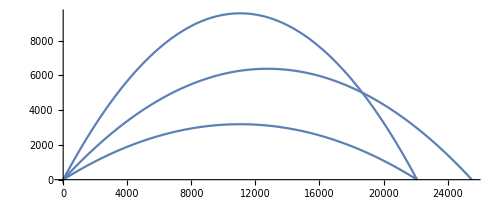

```mathematica
Show[{a, b, c} , PlotRange -> All]
```

(c) A torus can be expressed parametrically as
x = (a + b cos v) cos u
y = (a + b cos v) sin u
z = b sin v

Plot the torus for a = 5 , b = 2 and 0 ≤ u ≤ 2π and 0 ≤ v ≤ 2π and use
rainbow color function .

```mathematica
Clear["Global`*"]
x[u_, v_] = (a + b Cos[v]) Cos[u];
y[u_,v_] = (a + b Cos[v]) Sin[u];
z[u_, v_] = b  Sin[v];
a = 5;
b = 2;
```

```mathematica
ParametricPlot3D[{x[u,v],y[u,v],z[u,v]}, {u, 0, 2π },{v , 0, 2π }, ColorFunction->"Rainbow"]
```

-Graphics3D-